```mathematica
(Series[1/(√((1/rm)^2(1-um^2)r^4- r^2(1-u^2)))/.{u->1/√r},{um,0,3}]//Normal)//FullSimplify
```

(2 rm^2-2 r rm^2+r^3 (2+um^2))/(2 √(r-r^2+r^4/rm^2) (r^3+rm^2-r rm^2))

```mathematica
1/(√((1/rm)^2(1-um^2)r^4- r^2(1-u^2)))/.{um->rt/rm,u->√(rt/r)}//FullSimplify
```

1/(√(r (-r+rt+(r^3 (rm-rt) (rm+rt))/rm^4)))

```mathematica
(rm-rt) (rm+rt)//ExpandAll
```

rm^2-rt^2

```mathematica
Integrate[(2 rm^2-2 r rm^2+r^3 (2+um^2))/(2 √(r-r^2+r^4/rm^2) (r^3+rm^2-r rm^2)),{r,1,∞}]
```

∫_1^∞ 1/(√(r (1-r+r^3)))ⅆr

```mathematica
(Series[1/(√((1/rm)^2(1-x^2)r^4- r^2(1-u^2))),{x,0,2}]//Normal)/.{u->1/√r,x->1/rm}//FullSimplify
```

(r^3+2 r^3 rm^2-2 (-1+r) rm^4)/(2 √(r-r^2+r^4/rm^2) rm^2 (r^3+rm^2-r rm^2))

```mathematica
result =Integrate[2(1+rt/(2rm)(r^3-rm^3)/(r(r^2-rm)))rm/(r √(r^2-rm^2)),{r,rm,∞}]
```

ConditionalExpression[π+rt+(π rt)/(2 √((-1+rm) rm))-(rm rt ArcCsc[√rm])/(√(-1+rm)), Re[rm]>1&&Im[rm]==0]

```mathematica
Normal[Series[result//Normal,{rm,∞,4}]]/.{rm->1/x}
```

π+(-(2 rt)/3+(π rt)/2) x+(-(8 rt)/15+(π rt)/4) x^2+(-(16 rt)/35+(3 π rt)/16) x^3+(-(128 rt)/315+(5 π rt)/32) x^4

```mathematica
%/.{x->0}
```

π

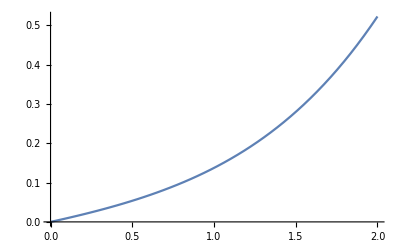

```mathematica
Plot[Normal[Series[result-π//Normal,{rm,∞,4}]]/.{rm->1/x,rt->0.1},{x,0,2},PlotRange->Full]
```